# MS-C1650 - Numerical Analysis Week 18: Lecture 5: Bezier Curves

## Harri Hakula, 2021

```mathematica
b[t_,n_,k_]:=Binomial[n,k] t^k(1-t)^(n-k) /;k≠0; (* Bernstein polynomials *)
b[t_,n_,k_]:=Binomial[n,k](1-t)^(n-k) /;k==0;
β[t_,n_,x_]:=Sum[x[[k+1]]b[t,n,k],{k,0,n}] (* Bezierin curve *)
```

### Cases

#### 1

```mathematica
controlPoints={{-0.60,-0.78},{-0.73,-0.03},{1.07,-0.47}}
```

{{-0.6,-0.78},{-0.73,-0.03},{1.07,-0.47}}

```mathematica
degree=Length[controlPoints]-1
```

2

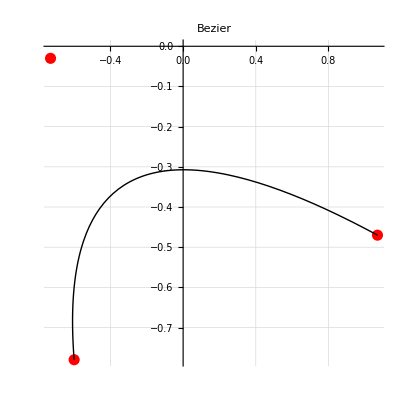

```mathematica
base=Show[ListPlot[controlPoints,PlotStyle->{Red,PointSize[0.02]}],ParametricPlot[{β[t,degree,controlPoints][[1]],β[t,degree,controlPoints][[2]]},{t,0,1},PlotStyle->{Thick,Black}],GridLines->Automatic,AspectRatio->1,PlotLabel->"Bezier"]
```

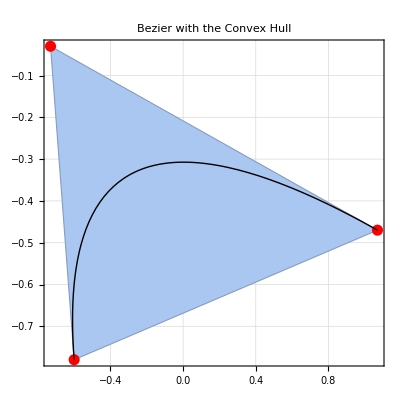

```mathematica
Show[ConvexHullMesh[controlPoints],base,Frame->True,GridLines->Automatic,AspectRatio->1,PlotLabel->"Bezier with the Convex Hull"]
```

#### 2

```mathematica
controlPoints={{-1,0},{1,4},{2,1}}
```

{{-1,0},{1,4},{2,1}}

```mathematica
degree=Length[controlPoints]-1
```

2

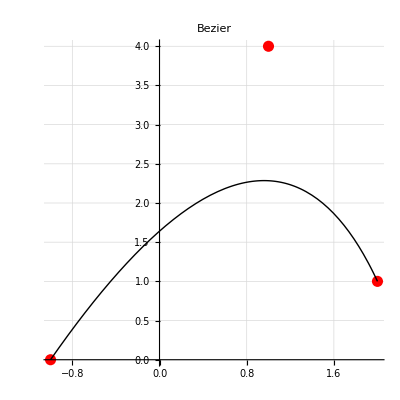

```mathematica
base=Show[ListPlot[controlPoints,PlotStyle->{Red,PointSize[0.02]}],ParametricPlot[{β[t,degree,controlPoints][[1]],β[t,degree,controlPoints][[2]]},{t,0,1},PlotStyle->{Thick,Black}],GridLines->Automatic,AspectRatio->1,PlotLabel->"Bezier"]
```

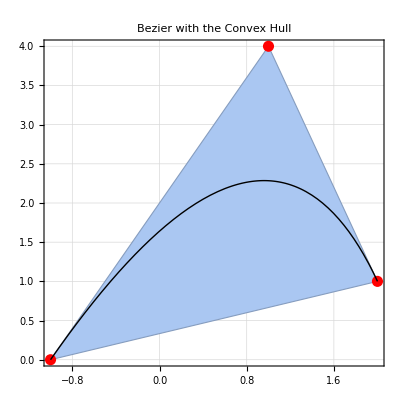

```mathematica
Show[ConvexHullMesh[controlPoints],base,Frame->True,GridLines->Automatic,AspectRatio->1,PlotLabel->"Bezier with the Convex Hull"]
```

#### 3

```mathematica
controlPoints={{-1,0},{1,4},{2,1},{-1,0}}
```

{{-1,0},{1,4},{2,1},{-1,0}}

```mathematica
degree=Length[controlPoints]-1
```

3

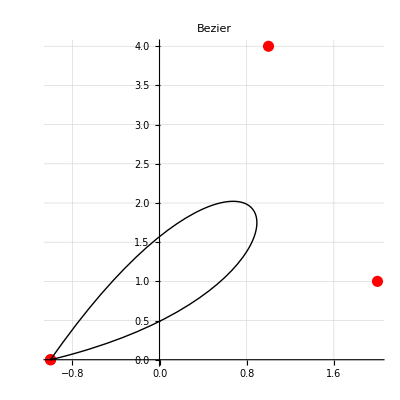

```mathematica
base=Show[ListPlot[controlPoints,PlotStyle->{Red,PointSize[0.02]}],ParametricPlot[{β[t,degree,controlPoints][[1]],β[t,degree,controlPoints][[2]]},{t,0,1},PlotStyle->{Thick,Black}],GridLines->Automatic,AspectRatio->1,PlotLabel->"Bezier"]
```

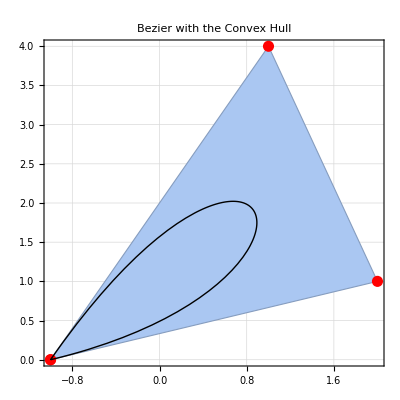

```mathematica
Show[ConvexHullMesh[controlPoints],base,Frame->True,GridLines->Automatic,AspectRatio->1,PlotLabel->"Bezier with the Convex Hull"]
```

#### 4

```mathematica
c=2
```

2

```mathematica
controlPoints={{-1,0},{1,4},{2,1},{-1-2/c,-4/c},{-1,0}}
```

{{-1,0},{1,4},{2,1},{-2,-2},{-1,0}}

```mathematica
degree=Length[controlPoints]-1
```

4

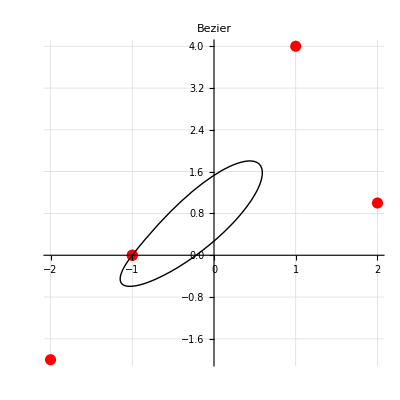

```mathematica
base=Show[ListPlot[controlPoints,PlotStyle->{Red,PointSize[0.02]}],ParametricPlot[{β[t,degree,controlPoints][[1]],β[t,degree,controlPoints][[2]]},{t,0,1},PlotStyle->{Thick,Black}],GridLines->Automatic,AspectRatio->1,PlotLabel->"Bezier"]
```

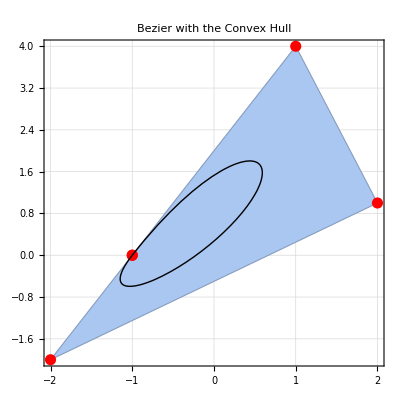

```mathematica
Show[ConvexHullMesh[controlPoints],base,Frame->True,GridLines->Automatic,AspectRatio->1,PlotLabel->"Bezier with the Convex Hull"]
```

### Lifting Algorithm

```mathematica
Lifting[cp:{{_?NumericQ,_?NumericQ}..}]:=Block[{pairs,n,ys},
n=Length[cp]-1;
pairs=Partition[cp,2,1];
ys=Table[(1-k/(n+1))cp[[k+1]]+k/(n+1)cp[[k]],{k,Length[pairs]}];
Join[{cp[[1]]},ys,{cp[[-1]]}]
]
```

#### 1

```mathematica
controlPoints={{-1,0},{1,4},{2,1}}
```

{{-1,0},{1,4},{2,1}}

```mathematica
degree=Length[controlPoints]-1
```

2

```mathematica
base=Show[ListPlot[controlPoints,PlotStyle->{Red,PointSize[0.02]}],ParametricPlot[{β[t,degree,controlPoints][[1]],β[t,degree,controlPoints][[2]]},{t,0,1},PlotStyle->{Thick,Black}],GridLines->Automatic,AspectRatio->1,PlotLabel->"Bezier"]
```

-Graphics-

```mathematica
Show[ConvexHullMesh[controlPoints],base,Frame->True,GridLines->Automatic,AspectRatio->1,PlotLabel->"Bezier with the Convex Hull"]
```

-Graphics-

```mathematica
cpList=NestList[Lifting,controlPoints,6];
```

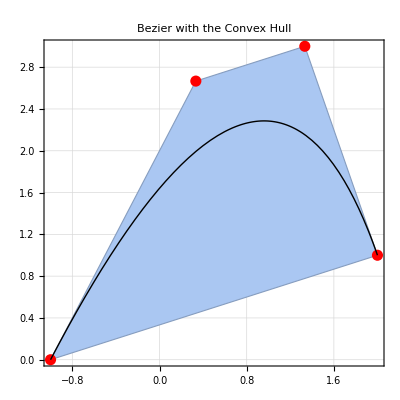
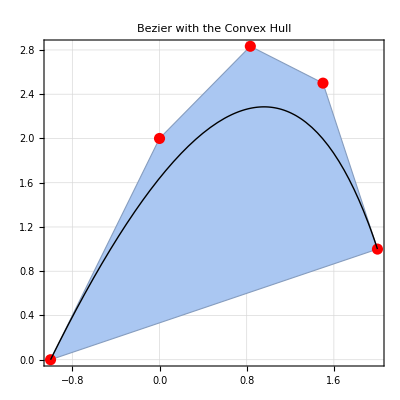
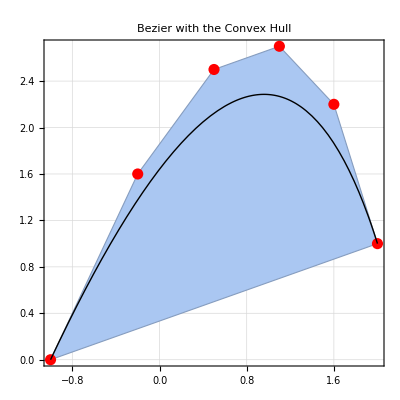
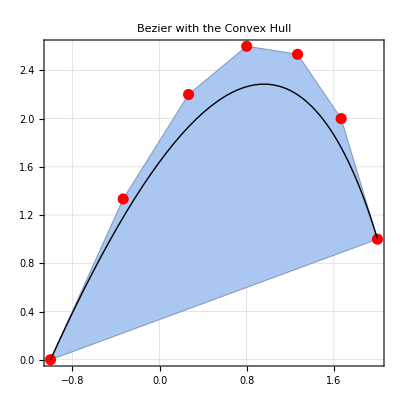
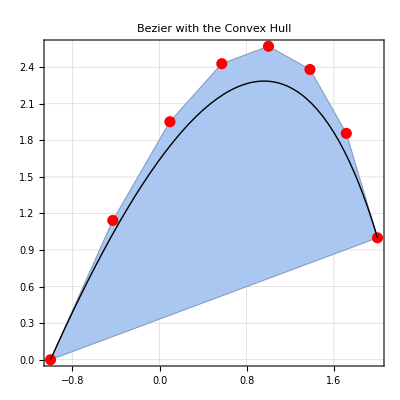
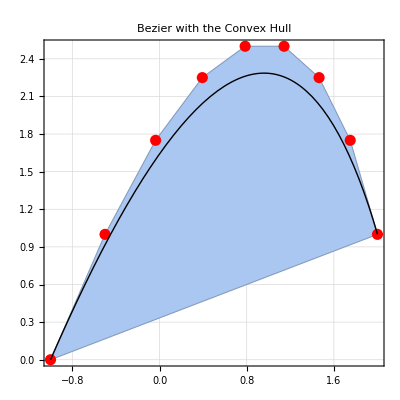
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
degree=Length[controlPoints]-1;
base=Show[ListPlot[controlPoints,PlotStyle->{Red,PointSize[0.02]}],ParametricPlot[{β[t,degree,controlPoints][[1]],β[t,degree,controlPoints][[2]]},{t,0,1},PlotStyle->{Thick,Black}],GridLines->Automatic,AspectRatio->1,PlotLabel->"Bezier"];
Show[ConvexHullMesh[controlPoints],base,Frame->True,GridLines->Automatic,AspectRatio->1,PlotLabel->"Bezier with the Convex Hull"],{controlPoints,cpList}]
```